```mathematica
n=7
b=2
a=-2
h=(b-a)/n
XDT={};YDT={};
For[i=0,i≤n,i++,
xdata[i]=a+i×h;
ydata[i]=N[Exp[-xdata[i]]];
XDT=Append[XDT,xdata[i]];
YDT=Append[YDT,ydata[i]];];
Array[xdata,{n+1,0}];
Array[ydata,{n+1,0}];
MatrixForm[XDT]MatrixForm[YDT]
```

7

2

-2

4/7

```mathematica
({{-2}, {-10/7}, {-6/7}, {-2/7}, {2/7}, {6/7}, {10/7}, {2}}) ({{7.38905609893065}, {4.172733883598096}, {2.3564184423836605}, {1.33071219744735}, {0.751477293075286}, {0.42437284567695}, {0.2396510364417758}, {0.1353352832366127}})
```

```mathematica
Array[difftab,{n+1,n+1},{0,0}];
For[k=1,k≤n,k++,
For[i=n,i≥n-k,i--,difftab[i,k]=""]];
For[i=0,i≤n,i++,difftab[i,0]=ydata[i]];
For [k=1, k≤n,k++,
For[i=0,i≤n-k,i++,
difftab[i,k]=(difftab[i+1,k-1]-difftab[i,k-1])/(xdata[i+k]-xdata[i])]];
tab1 = Array[difftab,{n+1,n+1}, {0,0}];
PaddedForm[TableForm[tab1],{6,5}]
```

7.38906 | -5.62856 |  2.14376 | -0.54433 |  0.10366 | -0.01579 |  0.00200 | -0.00022
 4.17273 | -3.17855 |  1.21062 | -0.30739 |  0.05854 | -0.00892 |  0.00113 | 
 2.35642 | -1.79499 |  0.68366 | -0.17359 |  0.03306 | -0.00504 |  | 
 1.33071 | -1.01366 |  0.38607 | -0.09803 |  0.01867 |  |  | 
 0.75148 | -0.57243 |  0.21802 | -0.05536 |  |  |  | 
 0.42437 | -0.32326 |  0.12312 |  |  |  |  | 
 0.23965 | -0.18255 |  |  |  |  |  | 
 0.13534 |  |  |  |  |  |  |

```mathematica
pln = difftab[0,0]+difftab[0,1]×(x-xdata[0]);
n=7;lst=List[pln];
For[k=2,k≤n,k++,
pln=lst[[k-1]]+difftab[0,k]×∏_(i=0)^(k-1) (x-xdata[i]);
lst=Append[lst,pln]];
nwtn[x_]:=N[lst[[n]]];
ColumnForm[lst]
```

7.38906-5.62856 (2+x)
7.38906-5.62856 (2+x)+2.14376 (10/7+x) (2+x)
7.38906-5.62856 (2+x)+2.14376 (10/7+x) (2+x)-0.544332 (6/7+x) (10/7+x) (2+x)
7.38906-5.62856 (2+x)+2.14376 (10/7+x) (2+x)-0.544332 (6/7+x) (10/7+x) (2+x)+0.10366 (2/7+x) (6/7+x) (10/7+x) (2+x)
7.38906-5.62856 (2+x)+2.14376 (10/7+x) (2+x)-0.544332 (6/7+x) (10/7+x) (2+x)+0.10366 (2/7+x) (6/7+x) (10/7+x) (2+x)-0.0157925 (-2/7+x) (2/7+x) (6/7+x) (10/7+x) (2+x)
7.38906-5.62856 (2+x)+2.14376 (10/7+x) (2+x)-0.544332 (6/7+x) (10/7+x) (2+x)+0.10366 (2/7+x) (6/7+x) (10/7+x) (2+x)-0.0157925 (-2/7+x) (2/7+x) (6/7+x) (10/7+x) (2+x)+0.00200497 (-6/7+x) (-2/7+x) (2/7+x) (6/7+x) (10/7+x) (2+x)
7.38906-5.62856 (2+x)+2.14376 (10/7+x) (2+x)-0.544332 (6/7+x) (10/7+x) (2+x)+0.10366 (2/7+x) (6/7+x) (10/7+x) (2+x)-0.0157925 (-2/7+x) (2/7+x) (6/7+x) (10/7+x) (2+x)+0.00200497 (-6/7+x) (-2/7+x) (2/7+x) (6/7+x) (10/7+x) (2+x)-0.000218182 (-10/7+x) (-6/7+x) (-2/7+x) (2/7+x) (6/7+x) (10/7+x) (2+x)

```mathematica
ColumnForm[Collect[lst,x]]
```

-3.86807-5.62856 x
2.25696+1.72147 x+2.14376 x^2
0.923901-1.43343 x-0.18909 x^2-0.544332 x^3
0.996433-1.00791 x+0.538648 x^2-0.0704562 x^3+0.10366 x^4
0.99959-1.00044 x+0.505497 x^2-0.160699 x^3+0.0359781 x^4-0.0157925 x^5
0.999933-1.00003 x+0.500941 x^2-0.166311 x^3+0.0400699 x^4-0.00891831 x^5+0.00200497 x^6
0.999987-0.999999 x+0.500188 x^2-0.166687 x^3+0.0413166 x^4-0.00829493 x^5+0.00156861 x^6-0.000218182 x^7

```mathematica
data = {{-2,7.38905609893065},{-10/7,4.172733883598096},{-6/7,2.3564184423836605},{-2/7,1.33071219744735},{2/7,0.751477293075286},{6/7,0.42437284567695},{10/7,0.2396510364417758},{2,0.1353352832366127}}
inpln:=InterpolatingPolynomial[data,x];
Collect[inpln,x]
```

{{-2,7.38906},{-10/7,4.17273},{-6/7,2.35642},{-2/7,1.33071},{2/7,0.751477},{6/7,0.424373},{10/7,0.239651},{2,0.135335}}

0.999987-0.999999 x+0.500188 x^2-0.166687 x^3+0.0413166 x^4-0.00829493 x^5+0.00156861 x^6-0.000218182 x^7

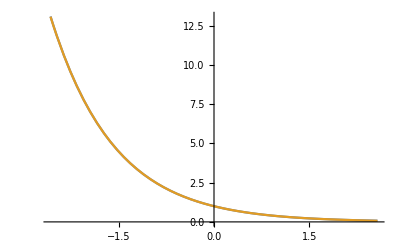

```mathematica
Plot[{Exp[-x],nwtn[x_]},{x,a-h,b+h}]
```

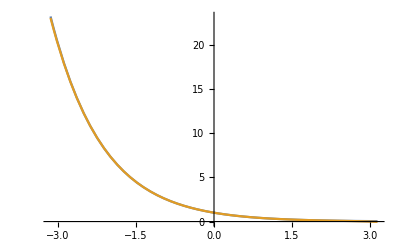

```mathematica
Plot[{Exp[-x],nwtn[x_]},{x,a-2h,b+2h}]
```

```mathematica
Pln={};P[n+1]=0;
For[i=n,i≥0,i--,P[i]=difftab[0,i]+(x-xdata[i])P[i+1];
Pln=Append[Pln,P[i]];]
ColumnForm[Pln]
```

-0.000218182
0.00200497-0.000218182 (-10/7+x)
-0.0157925+(0.00200497-0.000218182 (-10/7+x)) (-6/7+x)
0.10366+(-0.0157925+(0.00200497-0.000218182 (-10/7+x)) (-6/7+x)) (-2/7+x)
-0.544332+(0.10366+(-0.0157925+(0.00200497-0.000218182 (-10/7+x)) (-6/7+x)) (-2/7+x)) (2/7+x)
2.14376+(6/7+x) (-0.544332+(0.10366+(-0.0157925+(0.00200497-0.000218182 (-10/7+x)) (-6/7+x)) (-2/7+x)) (2/7+x))
-5.62856+(10/7+x) (2.14376+(6/7+x) (-0.544332+(0.10366+(-0.0157925+(0.00200497-0.000218182 (-10/7+x)) (-6/7+x)) (-2/7+x)) (2/7+x)))
7.38906+(2+x) (-5.62856+(10/7+x) (2.14376+(6/7+x) (-0.544332+(0.10366+(-0.0157925+(0.00200497-0.000218182 (-10/7+x)) (-6/7+x)) (-2/7+x)) (2/7+x))))

```mathematica
P[0]
```

7.38906+(2+x) (-5.62856+(10/7+x) (2.14376+(6/7+x) (-0.544332+(0.10366+(-0.0157925+(0.00200497-0.000218182 (-10/7+x)) (-6/7+x)) (-2/7+x)) (2/7+x))))

```mathematica
nwtn[x_]:=P[0];
m=70
XDAT={};YDAT={};nwtnDAT={};MR={};
For[i=0,i≤m,i++,
xdatas[i]=a+i×(h/10);
ydatas[i]=N[Exp[-xdatas[i]]];
x=xdatas[i];
nwtndatas[i]=nwtn[i];
mr[i]=Abs[ydatas[i]-nwtndatas[i]];
XDAT=Append[XDAT,xdatas[i]];
YDAT=Append[YDAT, ydatas[i]];
nwtnDAT=Append[nwtnDAT,nwtndatas[i]];
MR=Append[MR,mr[i]];];
MatrixForm[N[XDAT]]MatrixForm[N[YDAT]]MatrixForm[N[nwtnDAT]]MatrixForm[MR]
```

70

(-2.
-1.94286
-1.88571
-1.82857
-1.77143
-1.71429
-1.65714
-1.6
-1.54286
-1.48571
-1.42857
-1.37143
-1.31429
-1.25714
-1.2
-1.14286
-1.08571
-1.02857
-0.971429
-0.914286
-0.857143
-0.8
-0.742857
-0.685714
-0.628571
-0.571429
-0.514286
-0.457143
-0.4
-0.342857
-0.285714
-0.228571
-0.171429
-0.114286
-0.0571429
0.
0.0571429
0.114286
0.171429
0.228571
0.285714
0.342857
0.4
0.457143
0.514286
0.571429
0.628571
0.685714
0.742857
0.8
0.857143
0.914286
0.971429
1.02857
1.08571
1.14286
1.2
1.25714
1.31429
1.37143
1.42857
1.48571
1.54286
1.6
1.65714
1.71429
1.77143
1.82857
1.88571
1.94286
2.) (0.
0.00014818
0.000221156
0.000242235
0.00022953
0.000196822
0.000154321
0.00010932
0.0000667704
0.0000297742
0.
0.0000219603
0.0000362951
0.0000437275
0.0000453152
0.0000422905
0.0000359354
0.0000274872
0.0000180698
8.64802×10^-6
4.44089×10^-16
7.29427×10^-6
0.0000128522
0.0000164779
0.0000181434
0.000017965
0.0000161757
0.0000130958
9.10282×10^-6
4.60217×10^-6
2.22045×10^-16
4.32179×10^-6
8.02695×10^-6
0.0000108424
0.0000125717
0.0000131033
0.0000124152
0.0000105742
7.73093×10^-6
4.11058×10^-6
2.22045×10^-16
4.26892×10^-6
8.33849×10^-6
0.0000118468
0.0000144505
0.0000158488
0.0000158065
0.0000141764
0.0000109191
6.11968×10^-6
1.11022×10^-15
7.07513×10^-6
0.0000145983
0.0000219283
0.0000283087
0.0000328971
0.0000348075
0.000033166
0.0000271826
0.0000162398
5.82867×10^-16
0.0000214666
0.0000475324
0.0000768387
0.000107097
0.000134862
0.000155278
0.000161792
0.000145835
0.0000964695
2.10942×10^-15) (7.38906
6.97866
6.59106
6.22499
5.87925
5.55271
5.24431
4.95303
4.67794
4.41812
4.17273
3.94098
3.72209
3.51536
3.32012
3.13571
2.96155
2.79707
2.64172
2.49499
2.35642
2.22554
2.10193
1.98519
1.87493
1.77079
1.67244
1.57955
1.49182
1.40897
1.33071
1.2568
1.187
1.12107
1.05881
1.
0.944459
0.892003
0.84246
0.795669
0.751477
0.70974
0.67032
0.63309
0.597928
0.564718
0.533353
0.50373
0.475753
0.449329
0.424373
0.400803
0.378542
0.357517
0.337661
0.318907
0.301194
0.284466
0.268666
0.253744
0.239651
0.226341
0.213769
0.201897
0.190683
0.180092
0.17009
0.160643
0.151721
0.143294
0.135335) (7.38906
6.97881
6.59128
6.22523
5.87948
5.5529
5.24446
4.95314
4.678
4.41815
4.17273
3.94095
3.72206
3.51532
3.32007
3.13567
2.96152
2.79704
2.6417
2.49498
2.35642
2.22555
2.10195
1.98521
1.87495
1.77081
1.67246
1.57957
1.49183
1.40897
1.33071
1.2568
1.18699
1.12106
1.05879
0.999987
0.944447
0.891992
0.842453
0.795665
0.751477
0.709744
0.670328
0.633102
0.597942
0.564734
0.533369
0.503744
0.475764
0.449335
0.424373
0.400796
0.378527
0.357495
0.337632
0.318874
0.301159
0.284432
0.268639
0.253728
0.239651
0.226362
0.213817
0.201973
0.19079
0.180227
0.170245
0.160805
0.151866
0.14339
0.135335)

0.000242235

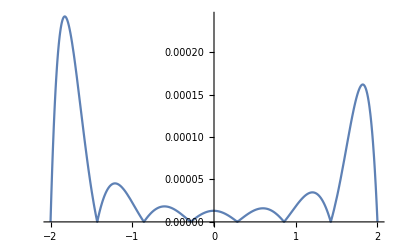

```mathematica
0.00024223454687977153
Plot[Abs[Exp[-x]-nwtn[x]],{x,-2,2}]
```

```mathematica
FindMaximum[{Abs[Exp[-x]-nwtn[x]],-2≤x≤2},{x}]
```

{0.000162014,{2→1.82043}}

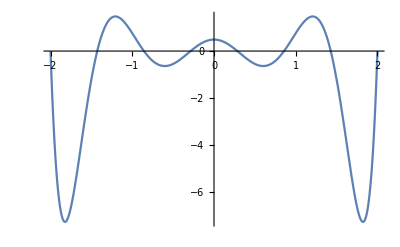

```mathematica
{0.0001620137378415265,{2->1.8204255437759231}}
Plot[∏_(i=0)^n (x-xdata[i]),{x,-2,2}]
```

```mathematica
FindMaximum[{∏_(i=0)^n (x-xdata[i]),-2≤x≤0},{x}]
```

```mathematica
{1.4749040152533832,{2->-1.2074687411948342}}
```

```mathematica
ⅇ^2/(8!)×1.4749040152533832
```

```mathematica
0.0002702913816777112
```

```mathematica
n1=8
b=2
a=-2
h=(b-a)/n1
XDT={};YDT={};
For[i=0,i≤n1,i++,
xdata1[i]=a+i×h;
ydata1[i]=N[Exp[-xdata1[i]]];
XDT=Append[XDT,xdata1[i]];
YDT=Append[YDT,ydata1[i]];];
Array[xdata1,{n1+1,0}];
Array[ydata1,{n1+1,0}];
MatrixForm[XDT]MatrixForm[YDT]
```

```mathematica
({{-2}, {-3/2}, {-1}, {-1/2}, {0}, {1/2}, {1}, {3/2}, {2}}) ({{7.38905609893065}, {4.4816890703380645}, {2.718281828459045}, {1.6487212707001282}, {1.}, {0.6065306597126334}, {0.36787944117144233}, {0.22313016014842982}, {0.1353352832366127}})
```

```mathematica
Array[difftab,{n1+1,n1+1},{0,0}];
For[k=1,k≤n1,k++,
For[i=n1,i≥n1-k,i--,difftab[i,k]=""]];
For[i=0,i≤n1,i++,difftab[i,0]=ydata1[i]];
For [k=1, k≤n1,k++,
For[i=0,i≤n1-k,i++,
difftab[i,k]=(difftab[i+1,k-1]-difftab[i,k-1])/(xdata1[i+k]-xdata1[i])]];
tab1 = Array[difftab,{n+1,n1+1}, {0,0}];
PaddedForm[TableForm[tab1],{6,5}]
```

7.38906 | -5.81473 |  2.28792 | -0.60015 |  0.11807 | -0.01858 |  0.00244 | -0.00027 |  0.00003
 4.48169 | -3.52681 |  1.38769 | -0.36401 |  0.07161 | -0.01127 |  0.00148 | -0.00017 | 
 2.71828 | -2.13912 |  0.84168 | -0.22078 |  0.04344 | -0.00684 |  0.00090 |  | 
 1.64872 | -1.29744 |  0.51050 | -0.13391 |  0.02635 | -0.00415 |  |  | 
 1.00000 | -0.78694 |  0.30964 | -0.08122 |  0.01598 |  |  |  | 
 0.60653 | -0.47730 |  0.18780 | -0.04926 |  |  |  |  | 
 0.36788 | -0.28950 |  0.11391 |  |  |  |  |  | 
 0.22313 | -0.17559 |  |  |  |  |  |  |

```mathematica
(f^(7)(ξ))/8!=0.00003
ξ=0.00003*8!
```

(f^7 ξ)/8≠0.00003

1.2096

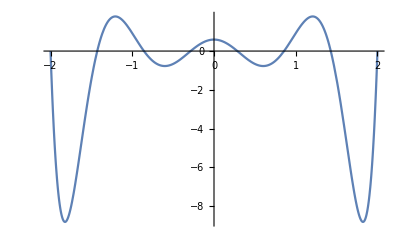

```mathematica
1.2096
Plot[1.2096*∏_(i=0)^n (x-xdata[i]),{x,-2,2}]
```

```mathematica
FindMaximum[{1.2096*∏_(i=0)^n (x-xdata[i]),-2≤x≤-1},{x}]
```

```mathematica
{1.7840438968504941,{2->-1.2074687388121959}}
```